# Tesis Sara v4.0

## Inicialización

```mathematica
Needs["AdvancedMapping`"];
```

```mathematica
RCM[ca_]:=Block[{n =Length[ca]},N[Abs[1/n Sum[ca[[i]](i-n/2),{i,1,n}]]]];
Returns[x_,Δt_]:= DeleteCases[N[Log[Drop[x,Δt]]-Log[Take[x,{1,-(1+Δt)}]]],Indeterminate];
CATimeSeries[rule_,states_,radius_,size_,iterations_]:=Map[RCM,CellularAutomaton[{rule,states,radius},RandomInteger[states-1,size],iterations]];
```

```mathematica
RCM[RandomInteger[2,10]]
```

0.6

```mathematica
Manipulate[ArrayPlot[CellularAutomaton[{r,3,1},RandomInteger[2,100],100]],{r,1,65536,1}]
```

```mathematica
2^2^4
```

65536

```mathematica
RandomInteger[65536,10]
```

{23904,43003,27833,19535,18125,32636,35317,60254,13371,49641}

```mathematica
ret = Returns[CATimeSeries[44434,2,3,500,2000],1];
```

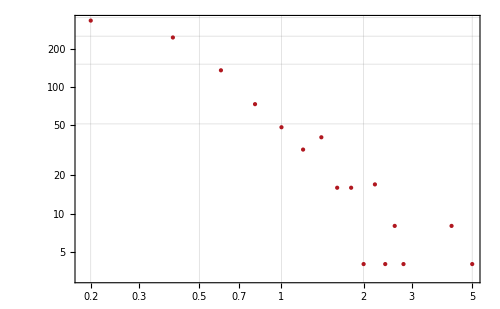

```mathematica
HistogramPointPlot[ret,ScalingFunctions->{"Log","Log"}]
```

```mathematica
Clear[HistogramPoints]
```

```mathematica
(* Opciones de estilo *)
smallFontSize = 13;
bigFontSize = 15;
plotSize = 500;
colors = {ColorData["Legacy"]["IndianRed"],Black,Blue,ColorData["Legacy"]["Olive"]};

HistogramPoints[data_,bspec_ : Automatic]:=Transpose[MapAt[Drop[#,1]&,HistogramList[data,bspec,"Count"],1]];
HistogramPointPlot[data_,opts: OptionsPattern[]]:=Block[{pltData = HistogramPoints[data]},
ListPlot[
pltData,
Joined->False,
Frame->True,
PlotTheme->"Monochrome",
BaseStyle->FontSize->14,
PlotStyle->{First[colors],{PointSize[Large],First[colors]}},
ImageSize->500,
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
FilterRules[{opts},Options[ListPlot]]
]
];
```

```mathematica
3^2^3
```

6561

```mathematica
reglasRandom = Sort@RandomInteger[65536-1,100]
```

{132,1681,2435,2480,3495,3901,4666,7410,9255,9456,10428,11507,11966,13580,13851,14358,14375,14770,14998,16203,16352,16368,16652,17059,17218,18458,18548,18639,18662,18684,18821,18849,19345,19366,19878,21558,22216,22469,22880,23370,23952,24269,24679,26077,26719,27208,28041,28679,28702,30115,31537,31624,32815,34406,36586,37149,38950,39051,39281,41188,41684,42290,42415,42806,42936,43202,45559,45980,46911,47553,48087,48978,49722,50206,50268,50389,51125,52400,52880,53529,53986,54864,56138,56776,57080,57332,57352,59001,59092,59687,59848,60064,60082,60917,60975,61545,61943,63354,64022,64201}

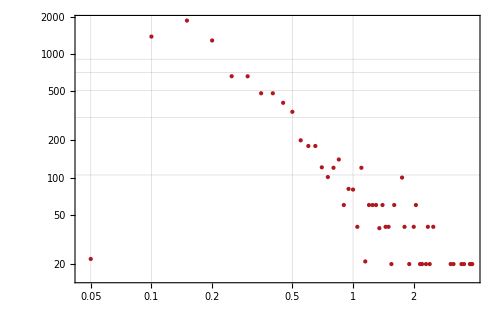

```mathematica
HistogramPointPlot[Abs[Returns[CATimeSeries[44434,2,3,500,10000],1]],ScalingFunctions->{"Log","Log"}]
```

```mathematica
FindDistribution[Abs[Returns[CATimeSeries[44434,2,3,500,10000],1]]]
```

MixtureDistribution[{0.745426,0.254574},{LogisticDistribution[0.315801,0.106215],GammaDistribution[4.55968,0.36774]}]

```mathematica
DistributionFitTest[Abs[Returns[CATimeSeries[44434,2,3,500,10000],1]],ParetoDistribution[a,b]]
```

2.34513×10^-16

```mathematica
DistributionFitTest[Abs[Returns[CATimeSeries[44434,2,3,500,10000],1]],PowerDistribution[a,b]]
```

2.07842×10^-16

```mathematica
DistributionFitTest[Abs[Returns[CATimeSeries[44434,2,3,500,10000],1]], LogisticDistribution[a,b]]
```

```mathematica
ProgressTable[HistogramPointPlot[Abs[Returns[CATimeSeries[r,3,1,100,10000],1]], ScalingFunctions->{"Log","Log"}],{r,reglasRandom}]
```

```mathematica
Hist=ProgressTable[HistogramPointPlot[Abs[Returns[CATimeSeries[r,3,1,100,10000],1]], ScalingFunctions->{"Log","Log"}],{r,reglasRandom}];
```

```mathematica
MapThread[Labeled[#1,#2,Top]&,{Hist,reglasRandom}]
```

```mathematica
Tuples[{0,1},3]
```

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}}

```mathematica
Δ = Map[{#,CellularAutomaton[30,#][[2]]}&,Tuples[{0,1},3]]
```

{{{0,0,0},0},{{0,0,1},1},{{0,1,0},1},{{0,1,1},1},{{1,0,0},1},{{1,0,1},0},{{1,1,0},0},{{1,1,1},0}}

```mathematica
N[Count[Δ,{_,1}]/Length[Δ]]
```

0.5

```mathematica
Range[0,1]
```

{0,1}

```mathematica
CalculateLambda[{rule_,states_,radius_},quiescent_ : 1]:=Block[{Δ},
Δ = Map[{#,CellularAutomaton[{rule,states,radius},#][[2]]}&,Tuples[Range[0,states-1],radius+2]];
N[Count[Δ,{_,quiescent}]/Length[Δ]]
];
```

```mathematica
CalculateLambda[{12376,3,1},2]
```

0.148148

```mathematica
randomRules = Sort[RandomInteger[7625597484987-1,1000]];
```

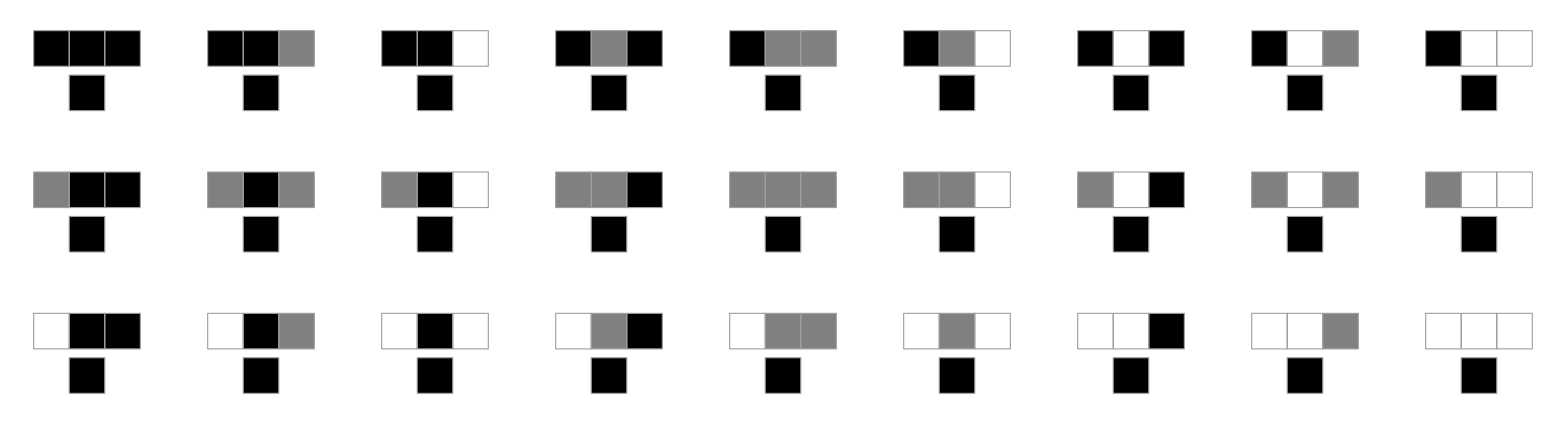

```mathematica
RulePlot[CellularAutomaton[{7625597484987-1,3,1}]]
```

```mathematica
3^3^3
```

7625597484987

```mathematica
sorted = SortBy[Table[{r,CalculateLambda[{r,3,1},2]},{r,randomRules}],Last];
```

```mathematica
reglasCriticas = Select[sorted,0.3<Last[#]<0.61&];
```

```mathematica
Table[ArrayPlot[CellularAutomaton[{r,3,1},RandomInteger[2,200],200],PlotLegends->{CalculateLambda[{r,3,1},2]}],{r,reglasCriticas[[All,1]]}]
```

```mathematica
StillOrPeriodicQ[l__]:=Block[{lista,pares},
lista = {l};
pares = DeleteDuplicatesBy[DeleteCases[Tuples[Range[Length[lista]],2],{x_,y_}/; x==y],Sort];
Apply[Or,Map[lista[[First[#]]]==lista[[Last[#]]]&,pares]]
];
Flip[0]=1;
Flip[1]=2;
Flip[2]=0;
Disturb[ca_]:=MapAt[Flip,ca,RandomInteger[{1,Length[ca]}]];
Relax[rule_,states_,radius_,configuration_,lookback_ :5,maxIterations_ :1000]:=NestWhileList[CellularAutomaton[{rule,states,radius},#]&,configuration,!StillOrPeriodicQ[##]&,lookback,maxIterations];
```

```mathematica
MeasureRelaxationTime[rule_,states_,radius_,stableConf_,lookback_ :5] := Block[{disturbed,relaxation},
disturbed = Disturb[stableConf];
relaxation = Relax[rule,states,radius,disturbed,lookback];
{Last[relaxation],Length[relaxation]}
];

GetStableConfiguration[rule_,states_,radius_,initialConfiguration_,lookback_ :5,maxIterations_ :1000]:=Block[{nested},
nested = NestWhileList[CellularAutomaton[{rule,states,radius},#]&,initialConfiguration,!StillOrPeriodicQ[##]&,lookback,maxIterations];
If[Length[nested]==1001,
Return[$Unstable],
Return[Last[nested]]
];
];
DisturbAndRelax[rule_,states_,radius_,cycles_,lookback_ :5]:=Block[{random,stableConf,relaxationTime,result},

random = RandomInteger[states-1,{100}];
stableConf = GetStableConfiguration[rule,states,radius,random,lookback,1000];
If[stableConf===$Unstable,Return[$Unstable]];

result =Table[
{stableConf, relaxationTime}=MeasureRelaxationTime[rule,states,radius,stableConf,lookback];
relaxationTime,
cycles
];
Return[result];
];
```

```mathematica
relaxTime = DisturbAndRelax[4154188013052,3,1,10000,5];
```

```mathematica
colors = {ColorData["Legacy"]["IndianRed"],Black,Blue,ColorData["Legacy"]["Olive"]};
HistogramPoints[data_]:=Map[{#,Count[data,#]}&,Sort[DeleteDuplicates[data]]];
HistogramPoints[data_,bspec_]:=Transpose[MapAt[Drop[#,1]&,HistogramList[data,bspec,"Count"],1]];
HistogramPointPlot[data_,opts: OptionsPattern[]]:=Block[{pltData = HistogramPoints[data]},
ListPlot[
pltData,
Joined->False,
Frame->True,
PlotTheme->"Monochrome",
BaseStyle->FontSize->14,
PlotStyle->{First[colors],{PointSize[Large],First[colors]}},
ImageSize->500,
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
FilterRules[{opts},Options[ListPlot]]
]
];
```

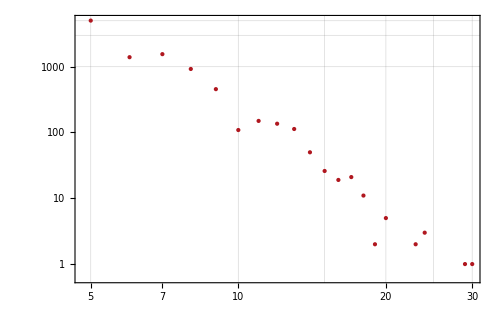

```mathematica
HistogramPointPlot[relaxTime,ScalingFunctions->{"Log","Log"}]
```